```mathematica
NotebookDirectory[]
```

/Users/flaxmans/Documents/Research/ProjectsWithPatrik/Regime_shifts/

```mathematica
f1AA=p1^2; (* frequency of AA genotype before migration in deme 1 *)
f1AB=2 p1*(1-p1); (* frequency of AB genotype before migration in deme 1 *)
f2AA=p2^2; (* frequency of AA genotype before migration in deme 2 *)
f2AB=2 p2*(1-p2); (* frequency of AB genotype before migration in deme 2 *)
f1AAm=f1AA-m*f1AA+m*f2AA; (* frequency of AA genotype after migration in deme 1 *)
f1ABm=f1AB-m*f1AB+m*f2AB; (* frequency of AB genotype after migration in deme 1 *)
f2AAm=f2AA-m*f2AA+m*f1AA; (* frequency of AA genotype after migration in deme 2 *)
f2ABm=f2AB-m*f2AB+m*f1AB; (* frequency of AB genotype after migration in deme 2 *)
wAA1=1+s; (* fitness of AA in deme 1 *)
wAB1=1+0.5 s; (* fitness of AB in deme 1 *)
wBB1=1; (* fitness of BB in deme 1 *)
wAA2=1; (* fitness of AA in deme 2 *)
wAB2=1+0.5 s; (* fitness of AB in deme 2 *)
wBB2=1+s; (* fitness of BB in deme 2 *)
wbar1=FullSimplify[(f1AAm*wAA1)+(f1ABm*wAB1)+((1-(f1AAm+f1ABm))*wBB1)];
(* average fitness in deme 1 *)
wbar2=FullSimplify[(f2AAm*wAA2)+(f2ABm*wAB2)+((1-(f2AAm+f2ABm))*wBB2)];
(* average fitness in deme 2 *)
p1next=FullSimplify[(f1AAm*wAA1/wbar1)+(0.5*f1ABm*wAB1/wbar1)];
p2next=FullSimplify[(f2AAm*wAA2/wbar2)+(0.5*f2ABm*wAB2/wbar2)];
sols=Solve[{p1next==p1,p2next==p2},{p1,p2}]
p1eq=FullSimplify[(p1/.(sols[[3]]))]
Plot3D[p1eq,{m,0.0001,0.5},{s,0.0001,0.5},PlotRange->{0.5,1},AxesLabel->{{"m","s","p1"},FontSize->14}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{p1→0.,p2→0.},{p1→1.,p2→1.},{p1→(0.5 (4. m-1. s+6. m s-1. √(16. m^2+16. m^2 s+s^2-4. m s^2+4. m^2 s^2)))/(-1. s+4. m s),p2→1/(2. m+2. m s)((m (4. m-1. s+6. m s-1. √(16. m^2+16. m^2 s+s^2-4. m s^2+4. m^2 s^2)))/(-1. s+4. m s)-(0.5 s (4. m-1. s+6. m s-1. √(16. m^2+16. m^2 s+s^2-4. m s^2+4. m^2 s^2)))/(-1. s+4. m s)+(m s (4. m-1. s+6. m s-1. √(16. m^2+16. m^2 s+s^2-4. m s^2+4. m^2 s^2)))/(-1. s+4. m s)-(1. m s^2 (4. m-1. s+6. m s-1. √(16. m^2+16. m^2 s+s^2-4. m s^2+4. m^2 s^2)))/(-1. s+4. m s)+(0.25 s (4. m-1. s+6. m s-1. √(16. m^2+16. m^2 s+s^2-4. m s^2+4. m^2 s^2))^2)/(-1. s+4. m s)^2-(0.25 s^2 (4. m-1. s+6. m s-1. √(16. m^2+16. m^2 s+s^2-4. m s^2+4. m^2 s^2))^2)/(-1. s+4. m s)^2+(1.5 m s^2 (4. m-1. s+6. m s-1. √(16. m^2+16. m^2 s+s^2-4. m s^2+4. m^2 s^2))^2)/(-1. s+4. m s)^2+(0.125 s^2 (4. m-1. s+6. m s-1. √(16. m^2+16. m^2 s+s^2-4. m s^2+4. m^2 s^2))^3)/(-1. s+4. m s)^3-(0.5 m s^2 (4. m-1. s+6. m s-1. √(16. m^2+16. m^2 s+s^2-4. m s^2+4. m^2 s^2))^3)/(-1. s+4. m s)^3)},{p1→(0.5 (4. m-1. s+6. m s+√(16. m^2+16. m^2 s+s^2-4. m s^2+4. m^2 s^2)))/(-1. s+4. m s),p2→1/(2. m+2. m s)((m (4. m-1. s+6. m s+√(16. m^2+16. m^2 s+s^2-4. m s^2+4. m^2 s^2)))/(-1. s+4. m s)-(0.5 s (4. m-1. s+6. m s+√(16. m^2+16. m^2 s+s^2-4. m s^2+4. m^2 s^2)))/(-1. s+4. m s)+(m s (4. m-1. s+6. m s+√(16. m^2+16. m^2 s+s^2-4. m s^2+4. m^2 s^2)))/(-1. s+4. m s)-(1. m s^2 (4. m-1. s+6. m s+√(16. m^2+16. m^2 s+s^2-4. m s^2+4. m^2 s^2)))/(-1. s+4. m s)+(0.25 s (4. m-1. s+6. m s+√(16. m^2+16. m^2 s+s^2-4. m s^2+4. m^2 s^2))^2)/(-1. s+4. m s)^2-(0.25 s^2 (4. m-1. s+6. m s+√(16. m^2+16. m^2 s+s^2-4. m s^2+4. m^2 s^2))^2)/(-1. s+4. m s)^2+(1.5 m s^2 (4. m-1. s+6. m s+√(16. m^2+16. m^2 s+s^2-4. m s^2+4. m^2 s^2))^2)/(-1. s+4. m s)^2+(0.125 s^2 (4. m-1. s+6. m s+√(16. m^2+16. m^2 s+s^2-4. m s^2+4. m^2 s^2))^3)/(-1. s+4. m s)^3-(0.5 m s^2 (4. m-1. s+6. m s+√(16. m^2+16. m^2 s+s^2-4. m s^2+4. m^2 s^2))^3)/(-1. s+4. m s)^3)}}

(m (0.5+0.75 s)-0.125 s-0.125 √(s^2-4. m s^2+4. m^2 (2.+1. s)^2))/((-0.25+1. m) s)

-Graphics3D-

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{p1→0.,p2→0.},{p1→1.,p2→1.},{p1→(0.5 (4. m-1. s+6. m s-1. √(16. m^2+16. m^2 s+s^2-4. m s^2+4. m^2 s^2)))/(-1. s+4. m s),p2→1/(2. m+2. m s)((m (4. m-1. s+6. m s-1. √(16. m^2+16. m^2 s+s^2-4. m s^2+4. m^2 s^2)))/(-1. s+4. m s)-(0.5 s (4. m-1. s+6. m s-1. √(16. m^2+16. m^2 s+s^2-4. m s^2+4. m^2 s^2)))/(-1. s+4. m s)+(m s (4. m-1. s+6. m s-1. √(16. m^2+16. m^2 s+s^2-4. m s^2+4. m^2 s^2)))/(-1. s+4. m s)-(1. m s^2 (4. m-1. s+6. m s-1. √(16. m^2+16. m^2 s+s^2-4. m s^2+4. m^2 s^2)))/(-1. s+4. m s)+(0.25 s (4. m-1. s+6. m s-1. √(16. m^2+16. m^2 s+s^2-4. m s^2+4. m^2 s^2))^2)/(-1. s+4. m s)^2-(0.25 s^2 (4. m-1. s+6. m s-1. √(16. m^2+16. m^2 s+s^2-4. m s^2+4. m^2 s^2))^2)/(-1. s+4. m s)^2+(1.5 m s^2 (4. m-1. s+6. m s-1. √(16. m^2+16. m^2 s+s^2-4. m s^2+4. m^2 s^2))^2)/(-1. s+4. m s)^2+(0.125 s^2 (4. m-1. s+6. m s-1. √(16. m^2+16. m^2 s+s^2-4. m s^2+4. m^2 s^2))^3)/(-1. s+4. m s)^3-(0.5 m s^2 (4. m-1. s+6. m s-1. √(16. m^2+16. m^2 s+s^2-4. m s^2+4. m^2 s^2))^3)/(-1. s+4. m s)^3)},{p1→(0.5 (4. m-1. s+6. m s+√(16. m^2+16. m^2 s+s^2-4. m s^2+4. m^2 s^2)))/(-1. s+4. m s),p2→1/(2. m+2. m s)((m (4. m-1. s+6. m s+√(16. m^2+16. m^2 s+s^2-4. m s^2+4. m^2 s^2)))/(-1. s+4. m s)-(0.5 s (4. m-1. s+6. m s+√(16. m^2+16. m^2 s+s^2-4. m s^2+4. m^2 s^2)))/(-1. s+4. m s)+(m s (4. m-1. s+6. m s+√(16. m^2+16. m^2 s+s^2-4. m s^2+4. m^2 s^2)))/(-1. s+4. m s)-(1. m s^2 (4. m-1. s+6. m s+√(16. m^2+16. m^2 s+s^2-4. m s^2+4. m^2 s^2)))/(-1. s+4. m s)+(0.25 s (4. m-1. s+6. m s+√(16. m^2+16. m^2 s+s^2-4. m s^2+4. m^2 s^2))^2)/(-1. s+4. m s)^2-(0.25 s^2 (4. m-1. s+6. m s+√(16. m^2+16. m^2 s+s^2-4. m s^2+4. m^2 s^2))^2)/(-1. s+4. m s)^2+(1.5 m s^2 (4. m-1. s+6. m s+√(16. m^2+16. m^2 s+s^2-4. m s^2+4. m^2 s^2))^2)/(-1. s+4. m s)^2+(0.125 s^2 (4. m-1. s+6. m s+√(16. m^2+16. m^2 s+s^2-4. m s^2+4. m^2 s^2))^3)/(-1. s+4. m s)^3-(0.5 m s^2 (4. m-1. s+6. m s+√(16. m^2+16. m^2 s+s^2-4. m s^2+4. m^2 s^2))^3)/(-1. s+4. m s)^3)}}

(m (0.5+0.75 s)-0.125 s-0.125 √(s^2-4. m s^2+4. m^2 (2.+1. s)^2))/((-0.25+1. m) s)

```mathematica
p1eq/.{m->0.05,s->0.02}
```

0.524704

{0.01,0.02,0.05,0.1}

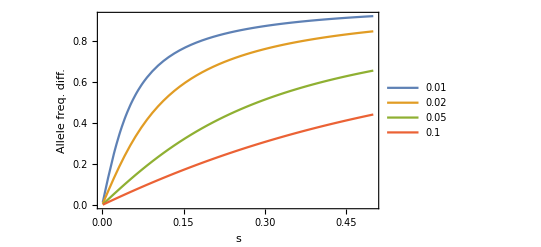

```mathematica
mvals={0.01,0.02,0.05,0.1}
toPlot=(p1eq-(1-p1eq))/.m->mvals;
Plot[Evaluate[toPlot],{s,0.001,0.5},PlotLegends->mvals,Frame->True,FrameLabel->{"s","Allele freq. diff."},BaseStyle->20]
```

```mathematica
toPlot
```

{-(4.16667 (0.01 (0.5+0.75 s)-0.125 s-0.125 √(0.96 s^2+0.0004 (2.+1. s)^2)))/s,-(4.34783 (0.02 (0.5+0.75 s)-0.125 s-0.125 √(0.92 s^2+0.0016 (2.+1. s)^2)))/s,-(4.54545 (0.03 (0.5+0.75 s)-0.125 s-0.125 √(0.88 s^2+0.0036 (2.+1. s)^2)))/s,-(4.7619 (0.04 (0.5+0.75 s)-0.125 s-0.125 √(0.84 s^2+0.0064 (2.+1. s)^2)))/s,-(5. (0.05 (0.5+0.75 s)-0.125 s-0.125 √(0.8 s^2+0.01 (2.+1. s)^2)))/s,-(5.26316 (0.06 (0.5+0.75 s)-0.125 s-0.125 √(0.76 s^2+0.0144 (2.+1. s)^2)))/s,-(5.55556 (0.07 (0.5+0.75 s)-0.125 s-0.125 √(0.72 s^2+0.0196 (2.+1. s)^2)))/s,-(5.88235 (0.08 (0.5+0.75 s)-0.125 s-0.125 √(0.68 s^2+0.0256 (2.+1. s)^2)))/s,-(6.25 (0.09 (0.5+0.75 s)-0.125 s-0.125 √(0.64 s^2+0.0324 (2.+1. s)^2)))/s,-(6.66667 (0.1 (0.5+0.75 s)-0.125 s-0.125 √(0.6 s^2+0.04 (2.+1. s)^2)))/s}

```mathematica
mvs
```

{0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}

```mathematica
ToString[mvals]
```

{0.01, 0.02, 0.03, 0.04, 0.05, 0.06, 0.07, 0.08, 0.09, 0.1}

{{s→(m (-0.5+1. p))/((0.25-0.25 p) p+m (0.5+p (-1.5+1. p)))}}

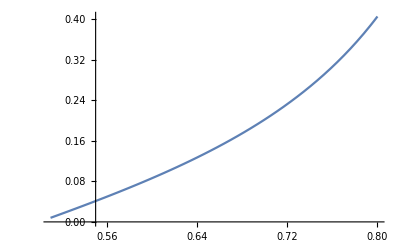

```mathematica
effectiveS=FullSimplify[Solve[p1eq==p,s]] (* this is Barton 1983's "s*" *)
Plot[((s/.effectiveS)/.m->0.05),{p,0.51,0.8}]
```

```mathematica
Plot3D[p1eq,{m,0.0001,0.5},{s,0.0001,1},PlotRange->{0,1},AxesLabel->{"m","s","(p̂)_1"},BaseStyle->{18,FontFamily->"Arial Black",FontColor->Black}]
```

-Graphics3D-

```mathematica
ht=2*0.5*0.5;
hs=2*p1*(1-p1);
fst=FullSimplify[((ht-hs)/ht)/.(p1->p1eq)]
Plot3D[fst,{m,0.00001,0.5},{s,0.00001,1},PlotRange->{0,1},AxesLabel->{"m","s","F_ST"},BaseStyle->{18,FontFamily->"Arial Black",FontColor->Black}]
```

(2. m^2+2. m^2 s+(0.0625+(-0.25+0.5 m) m) s^2-0.5 m √(s^2-4. m s^2+4. m^2 (2.+1. s)^2)-0.25 m s √(s^2-4. m s^2+4. m^2 (2.+1. s)^2))/((0.25-1. m)^2 s^2)

-Graphics3D-

```mathematica
W[L_,s_]:=Exp[L*s]
W2[L_,s_]:=(1+s)^L
Exp[Range[0,1,0.1]]
1.1^(Range[0,10])
```

{1.,1.10517,1.2214,1.34986,1.49182,1.64872,1.82212,2.01375,2.22554,2.4596,2.71828}

{1.,1.1,1.21,1.331,1.4641,1.61051,1.77156,1.94872,2.14359,2.35795,2.59374}

```mathematica
eqFreq[m_,s_]:=(m (0.5+0.75 s)-0.125 s-0.125 √(s^2-4. m s^2+4. m^2 (2.+1. s)^2))/((-0.25+1. m) s)
fitApprox[s_,n_]:=(1+0.5*s)^n

(* number of alleles is binomial with parameters 2L and eqFreq *)
avgFitAllIndep[L_,m_,s_]:=Sum[PDF[BinomialDistribution[2*L,eqFreq[m,s]],i]*fitApprox[s,i],{i,0,2*L}]
maxFit[L_,s_]:=(1+s)^L
minFit[L_,s_]:=1/maxFit[L,s]
avgScaled[L_,m_,s_]:=avgFitAllIndep[L,m,s]/maxFit[L,s]
hetScaled[L_,s_]:=((1+0.5 s)^L)/maxFit[L,s]
avgResident[L_,m_,s_]:=Sum[PDF[BinomialDistribution[2*L,eqFreq[m,s]],i]*fitApprox[s,i],{i,0,2*L}]
avgImmigrant[L_,m_,s_]:=Sum[PDF[BinomialDistribution[2*L,1-eqFreq[m,s]],i]*fitApprox[s,i],{i,0,2*L}]
```

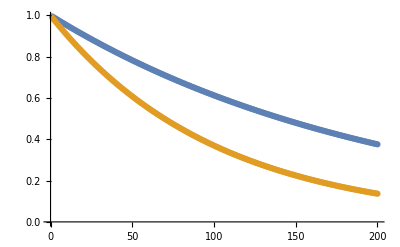

```mathematica
nLOCI=200;
sVal=0.01;
mVal=0.1;
avgFitVals=Table[avgScaled[L,mVal,sVal],{L,1,nLOCI}];
minFitVals=Table[minFit[L,sVal],{L,1,nLOCI}];
ListPlot[{Transpose[{Range[1,nLOCI],avgFitVals}],Transpose[{Range[1,nLOCI],minFitVals}]}]
```

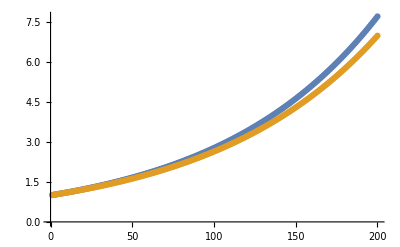

```mathematica
nLOCI=200;
sVal=0.02;
mVal=0.1;
avgResVals=Table[avgResident[L,mVal,sVal],{L,1,nLOCI}];
avgImmVals=Table[avgImmigrant[L,mVal,sVal],{L,1,nLOCI}];
ListPlot[{Transpose[{Range[1,nLOCI],avgResVals}],Transpose[{Range[1,nLOCI],avgImmVals}]}]
```

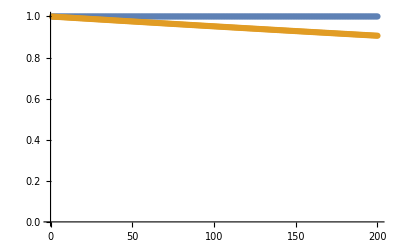

```mathematica
nLOCI=200;
sVal=0.01;
mVal=0.1;
avgResVals=Table[1,{L,1,nLOCI}];
avgImmVals=Table[avgImmigrant[L,mVal,sVal]/avgResident[L,mVal,sVal],{L,1,nLOCI}];
ListPlot[{Transpose[{Range[1,nLOCI],avgResVals}],Transpose[{Range[1,nLOCI],avgImmVals}]},PlotRange->{0,1}]
```

```mathematica
nLOCI=200;
sVal=0.02;
mVal=0.1;
maxFitVals=Table[1,{L,1,nLOCI}];
avgResVals=Table[avgResident[L,mVal,sVal]/maxFit[L,sVal],{L,1,nLOCI}];
avgImmVals=Table[avgImmigrant[L,mVal,sVal]/maxFit[L,sVal],{L,1,nLOCI}];
```

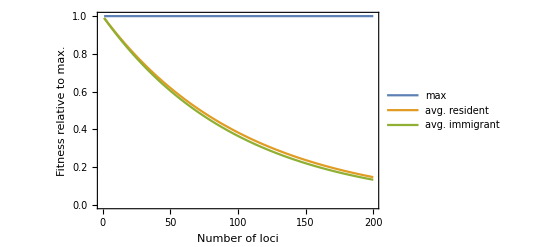

```mathematica
ListLinePlot[{Transpose[{Range[1,nLOCI],maxFitVals}],Transpose[{Range[1,nLOCI],avgResVals}],Transpose[{Range[1,nLOCI],avgImmVals}]},PlotRange->{0,1},Frame->True,FrameLabel->{"Number of loci","Fitness relative to max.","m = "<>ToString[mVal]<>", s = "<>ToString[sVal]},BaseStyle->14,PlotLegends->{"max","avg. resident","avg. immigrant"}]
```

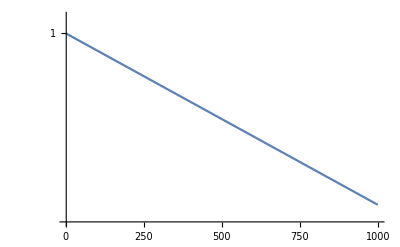

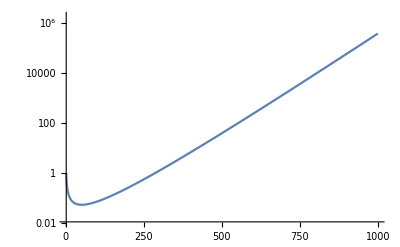

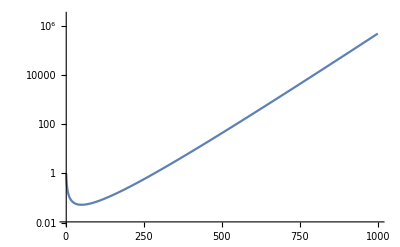

```mathematica
sVal = 0.02;
LogPlot[((1+sVal)^L)/Exp[0.5 sVal 2 L],{L,1,1000}]
LogPlot[((1+sVal)^L)/((1+0.5*sVal)^2*L),{L,1,1000}]
LogPlot[Exp[0.5 sVal 2 L]/((1+0.5*sVal)^2*L),{L,1,1000}]
```